Constantes y colores

```mathematica
<<MaTeX`
hEV=4.135667731;"eV*fs";
ℏEV=hEV/(2 π);
cUA=299.792458;"nm/fs";
αEF=0.0072973525693;

Rojo=RGBColor[0.65,0.25,0.22];
Cian=RGBColor[0.02,0.86,0.95];
Azul=RGBColor[0.02,0.47,0.75];
Verde=RGBColor[0,0.48,0.45];
Amarillo=RGBColor[1,0.7059,0];
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

Diferencia numérica entre Mathematica y C++

Datos:
T = 50 fs
n = 18 (2^n datos)

a = 1 nm
b = 3 nm
β = 0.58 (120 keV)

```mathematica
dataCpp=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/2.- Recoil Force/Resultados_Fuerza_de_retroceso_n18_T50_lmax1_a1_b3_beta58.txt","Table"];
Dimensions[dataCpp]
Table[{tiemposAl58PP[[j]],TablaFuerzaXAl58PP[[j]]},{j,Npuntos/2,Npuntos/2+2621}]//Dimensions
```

{2621,11}

{2622,2}

```mathematica
Transpose[{dataCpp[[2621,1]],dataCpp[[2621,2]]}]
{tiemposAl58PP[[Npuntos/2-1+2621]],TablaFuerzaXAl58PP[[Npuntos/2-1+2621]]}
```

{0.999451,-4.95129×10^-14}

{0.999451,-4.95129×10^-14}

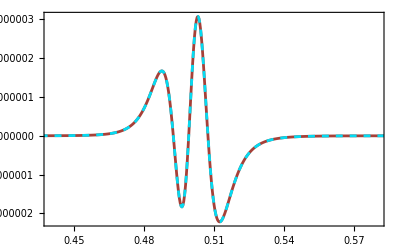

```mathematica
ComponenteTransversalMathvsCpp=ListPlot[{Transpose[{dataCpp[[All,1]],dataCpp[[All,2]]}],Table[{tiemposAl58PP[[j]],TablaFuerzaXAl58PP[[j]]},{j,Npuntos/2,Npuntos/2+2620}]},PlotRange->{{0.44,0.58},All},PlotStyle->{Rojo,{Cian,Dashed}},Joined->True,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["c(\\hbar\\alpha)^{-1}F_\\perp^\\text{ret}(t)\\text{ [PHz]}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{Mathematica}",FontSize->14],MaTeX["\\text{C++}",FontSize->14]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->0,LegendMargins->0,LegendMarkerSize->15],{0.75,0.70}]]
```

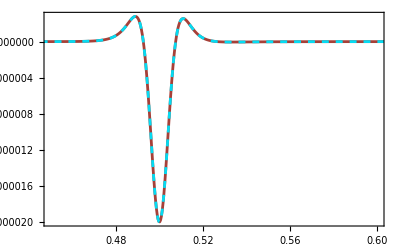

```mathematica
ComponenteLongitudinalMathvsCpp=ListPlot[{Transpose[{dataCpp[[All,1]],dataCpp[[All,3]]}],Table[{tiemposAl58PP[[j]],TablaFuerzaZAl58PP[[j]]},{j,Npuntos/2,Npuntos/2+2621}]},PlotRange->{{0.45,0.6},All},PlotStyle->{Rojo,{Cian,Dashed}},Joined->True,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["c(\\hbar\\alpha)^{-1}F_\\perp^\\text{ret}(t)\\text{ [PHz]}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{Mathematica}",FontSize->14],MaTeX["\\text{C++}",FontSize->14]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->0,LegendMargins->0,LegendMarkerSize->15],{0.75,0.30}]]
```

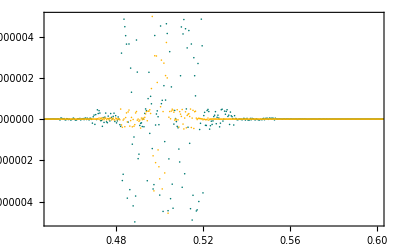

```mathematica
DiferenciaMathvsCpp=ListPlot[{Table[{dataCpp[[j,1]],10^6*(TablaFuerzaXAl58PP[[Npuntos/2-1+j]]-dataCpp[[j,2]])},{j,1,2621}],Table[{dataCpp[[j,1]],10^5*(TablaFuerzaZAl58PP[[Npuntos/2-1+j]]-dataCpp[[j,3]])},{j,1,2621}]},PlotRange->{{0.45,0.6},All},PlotStyle->{Verde,Amarillo},Joined->False,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["\\text{Cifra significativa}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{Comp. trans.}",FontSize->14],MaTeX["\\text{Comp. long.}",FontSize->14]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->0,LegendMargins->0,LegendMarkerSize->15],{0.75,0.75}]]
```

```mathematica
Export["ComponenteTransversalMathvsCpp.png",ComponenteTransversalMathvsCpp,ImageResolution->200];
Export["ComponenteLongitudinalMathvsCpp.png",ComponenteLongitudinalMathvsCpp,ImageResolution->200];
Export["DiferenciaMathvsCpp.png",DiferenciaMathvsCpp,ImageResolution->200];
```

Contribución cuadrupolar vs dipolar a la fuerza de retroceso e integral numérica

Datos:
T = 1,500 fs
n = 23 (2^n datos)

a = 1 nm
b = 3 nm
β = 0.58 (120 keV)

```mathematica
data1=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/2.- Recoil Force/Resultados_Fuerza_de_retroceso_n23_T1500_lmax1_a1_b3_beta58.txt","Table"];
data2=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/2.- Recoil Force/Resultados_Fuerza_de_retroceso_n23_T1500_lmax2_a1_b3_beta58.txt","Table"];
data3=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/2.- Recoil Force/Resultados_Fuerza_de_retroceso_n23_T1500_lmax3_a1_b3_beta58.txt","Table"];
Dimensions[data3]
Dimensions[data2]
Dimensions[data1]
```

{559,11}

{559,11}

{559,11}

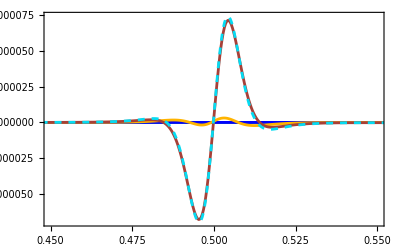

```mathematica
ComponenteTransversal=ListPlot[{Transpose[{data2[[All,1]],10^0*(data2[[All,2]]-data1[[All,2]])}],Transpose[{data2[[All,1]],10^0*data2[[All,6]]}],Transpose[{data1[[All,1]],data1[[All,2]]}],Transpose[{data2[[All,1]],10^0*data2[[All,4]]}],Transpose[{data2[[All,1]],data2[[All,2]]+data2[[All,4]]+data2[[All,6]]}]},PlotRange->{{0.45,0.55},All},PlotStyle->{Verde,Blue,Amarillo,Rojo,{Cian,Dashed}},Joined->True,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["c(\\hbar\\alpha)^{-1}F_\\perp^\\text{ret}(t)\\text{ [PHz]}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{ DE-DM}(\\times 10)",FontSize->8],MaTeX["\\text{  QE-QM}(\\times 10^3)",FontSize->8],MaTeX["\\text{  DE-QE}",FontSize->8],MaTeX["\\text{  DM-QM}(\\times 10^3)",FontSize->8],MaTeX["\\text{  Total}",FontSize->8]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->-0.3,LegendMargins->-3,LegendMarkerSize->15],{0.83,0.75}]]
```

```mathematica
FretDipDip=Interpolation[Transpose[{data1[[All,1]],data1[[All,2]]}]];
FretCuadCuad=Interpolation[Transpose[{data2[[All,1]],data2[[All,2]]-data1[[All,2]]}]];
FretDipECuadE=Interpolation[Transpose[{data2[[All,1]],data2[[All,4]]}]];
FretDipMCuadM=Interpolation[Transpose[{data2[[All,1]],data2[[All,6]]}]];
```

```mathematica
IntDEDM=NIntegrate[FretDipDip[x],{x,0.401,0.599},Method->"GaussKronrodRule"]
IntQEQM=NIntegrate[FretCuadCuad[x],{x,0.401,0.599},Method->"GaussKronrodRule"]
IntDEQE=NIntegrate[FretDipECuadE[x],{x,0.401,0.599},Method->"GaussKronrodRule"]
IntDMQM=NIntegrate[FretDipMCuadM[x],{x,0.401,0.599},Method->"GaussKronrodRule"]
```

2.73232×10^-10

2.2641×10^-14

-1.38437×10^-8

-3.58034×10^-15

```mathematica
IntTot=IntDEDM+IntQEQM+IntDEQE+IntDMQM
```

-1.35704×10^-8

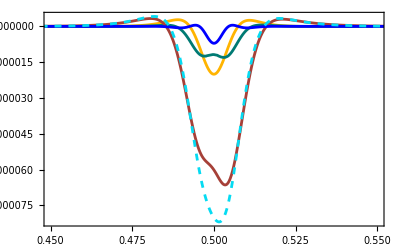

```mathematica
ComponenteLongitudinal=ListPlot[{Transpose[{data1[[All,1]],data1[[All,3]]}],Transpose[{data2[[All,1]],10^3*(data2[[All,3]]-data1[[All,3]])}],Transpose[{data2[[All,1]],10^0*data2[[All,5]]}],Transpose[{data2[[All,1]],10^3*data2[[All,7]]}],Transpose[{data2[[All,1]],data2[[All,3]]+data2[[All,5]]+data2[[All,7]]}]},PlotRange->{{0.45,0.55},All},PlotStyle->{Amarillo,Verde,Rojo,Blue,{Cian,Dashed}},Joined->True,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["c(\\hbar\\alpha)^{-1}F_\\|^\\text{ret}(t)\\text{ [PHz]}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{  DE-DM }",FontSize->8],MaTeX["\\text{  QE-QM }(\\times 10^3)",FontSize->8],MaTeX["\\text{  DE-QE}",FontSize->8],MaTeX["\\text{  DM-QM }(\\times 10^3)",FontSize->8],MaTeX["\\text{ total}",FontSize->8]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->-0.3,LegendMargins->-3,LegendMarkerSize->15],{0.83,0.25}]]
```

```mathematica
FretLongDEDM=Interpolation[Transpose[{data1[[All,1]],data1[[All,3]]}]];
FretLongQEQM=Interpolation[Transpose[{data2[[All,1]],data2[[All,3]]-data1[[All,3]]}]];
FretLongDEQE=Interpolation[Transpose[{data2[[All,1]],data2[[All,5]]}]];
FretLongDMQM=Interpolation[Transpose[{data2[[All,1]],data2[[All,7]]}]];
```

```mathematica
IntTranDEDM=NIntegrate[FretLongDEDM[x],{x,0.401,0.599},Method->{"GaussKronrodRule","Points"->100}]
IntTranQEQM=NIntegrate[FretLongQEQM[x],{x,0.401,0.599},Method->{"GaussKronrodRule","Points"->100}]
IntTranDEQE=NIntegrate[FretLongDEQE[x],{x,0.401,0.599},Method->{"GaussKronrodRule","Points"->100}]
IntTranDMQM=NIntegrate[FretLongDMQM[x],{x,0.401,0.599},Method->{"GaussKronrodRule","Points"->100}]
```

-1.16901×10^-7

-1.78269×10^-10

-1.02431×10^-6

-3.81275×10^-11

```mathematica
IntTot=IntDEDM+IntQEQM+IntDEQE+IntDMQM
```

```mathematica
Export["ComponenteTransversal.png",ComponenteTransversal,ImageResolution->200];
Export["ComponenteLongitudinal.png",ComponenteLongitudinal,ImageResolution->200];
```

Aproximación de los coeficientes de Mie para partícula pequeña

```mathematica
DLAF[l_,m_,x_]:=(l-m+1)/(x^2-1)LegendreP[l+1,m,x]-(l+1)x/(x^2-1)LegendreP[l,m,x];
DSBJ[l_,ρ_]:=(l/(2l+1))SphericalBesselJ[l-1,ρ]-((l+1)/(2l+1))SphericalBesselJ[l+1,ρ];
DSHP[l_,ρ_]:=(l/(2l+1))SphericalHankelH1[l-1,ρ]-((l+1)/(2l+1))SphericalHankelH1[l+1,ρ]

Hplus[l_,ρ_]:=ⅈ*SphericalHankelH1[l,ρ];
DHplus[l_,ρ_]:=ⅈ*DSHP[l,ρ];

psi[l_,ρ_]:=ρ*SphericalBesselJ[l,ρ];
Dpsi[l_,ρ_]:=ρ*DSBJ[l,ρ]+SphericalBesselJ[l,ρ];
xi[l_,ρ_]:=ρ*Hplus[l,ρ];
Dxi[l_,ρ_]:=ρ*DHplus[l,ρ]+Hplus[l,ρ];
```

```mathematica
tlE[l_,Nm_,x_]:=(-(Nm*psi[l,Nm*x]*Dpsi[l,x]-psi[l,x]*Dpsi[l,Nm*x]))/
(Nm*psi[l,Nm*x]*Dxi[l,x]-xi[l,x]*Dpsi[l,Nm*x]);
tlM[l_,Nm_,x_]:=(-(psi[l,Nm*x]*Dpsi[l,x]-Nm*psi[l,x]*Dpsi[l,Nm*x]))/
(psi[l,Nm*x]*Dxi[l,x]-Nm*xi[l,x]*Dpsi[l,Nm*x]);
```

```mathematica
Series[tlE[1,Nm,x],{x,0,5}]
Series[tlM[1,Nm,x],{x,0,5}]
Series[tlE[2,Nm,x],{x,0,7}]
Series[tlM[2,Nm,x],{x,0,7}]
```

(2 (-1+Nm^2) x^3)/(3 (2+Nm^2))+(2 (2-3 Nm^2+Nm^4) x^5)/(5 (2+Nm^2)^2)+O[x]^6

1/45 (-1+Nm^2) x^5+O[x]^6

((-1+Nm^2) x^5)/(15 (3+2 Nm^2))+((1-Nm^2) x^7)/(21 (3+2 Nm^2)^2)+O[x]^8

((-1+Nm^2) x^7)/1575+O[x]^8

```mathematica
γvel[β_]:=1/(√(1-β^2));
Kbessel[m_,b_,β_,ℏω_]:=BesselK[m,(ℏω*b)/(ℏEV*cUA*β*γvel[β])];
```

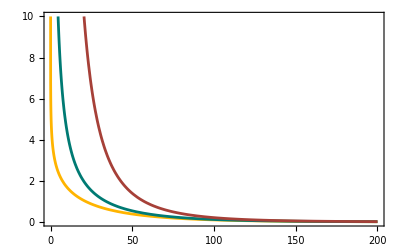

```mathematica
BesselKs=Plot[{Kbessel[0,3,0.58,ℏω],Kbessel[1,3,0.58,ℏω],Kbessel[2,3,0.58,ℏω]},{ℏω,0,200},PlotRange->{0,10},PlotStyle->{Amarillo,Verde,Rojo,Blue,{Cian,Dashed}},PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["K_m(\\omega b/c\\beta\\gamma)",FontSize->16],None},{MaTeX["\\hbar\\omega\\text{ [eV]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["m=0",FontSize->12],MaTeX["m=1",FontSize->12],MaTeX["m=2",FontSize->12]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->0,LegendMargins->-3,LegendMarkerSize->15],{0.83,0.75}]]
```

```mathematica
Export["BesselKs.png",BesselKs,ImageResolution->200];
```

```mathematica
data1=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/2.- Recoil Force/Resultados_Fuerza_de_retroceso_n22_T1000_lmax1_a1_b10_beta58.txt","Table"];
data2=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/2.- Recoil Force/Resultados_Fuerza_de_retroceso_n22_T1000_lmax2_a1_b10_beta58.txt","Table"];
dataNTSPA=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/2.- Recoil Force/Resultados_Fuerza_de_retroceso_NTSPA_n22_T1000_a1_b10_beta58.txt","Table"];
Dimensions[dataNTSPA]
```

{420,7}

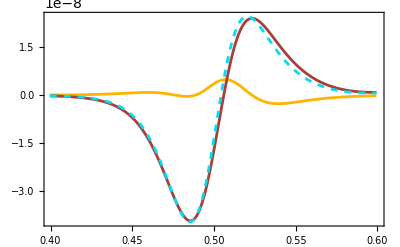

```mathematica
ComponenteTransversalNTSPA=ListPlot[{Transpose[{dataNTSPA[[All,1]],dataNTSPA[[All,2]]}],Transpose[{dataNTSPA[[All,1]],dataNTSPA[[All,4]]}],Transpose[{dataNTSPA[[All,1]],dataNTSPA[[All,6]]}]},PlotRange->{{0.4,0.6},All},PlotStyle->{Amarillo,Rojo,{Cian,Dashed}},Joined->True,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["c(\\hbar\\alpha)^{-1}F_\\perp^\\text{ret}(t)\\text{ [PHz]}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{ DE-DM}",FontSize->8],MaTeX["\\text{  DE-QE}",FontSize->8],MaTeX["\\text{  Total}",FontSize->8]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->-0.3,LegendMargins->-3,LegendMarkerSize->15],{0.83,0.75}]]
```

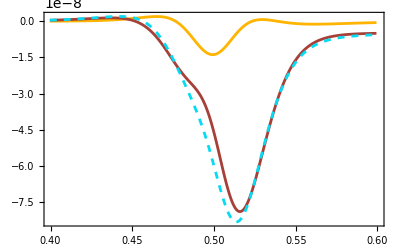

```mathematica
ComponenteLongitudinalNTSPA=ListPlot[{Transpose[{dataNTSPA[[All,1]],dataNTSPA[[All,3]]}],Transpose[{dataNTSPA[[All,1]],dataNTSPA[[All,5]]}],Transpose[{dataNTSPA[[All,1]],dataNTSPA[[All,7]]}]},PlotRange->{{0.4,0.6},All},PlotStyle->{Amarillo,Rojo,{Cian,Dashed}},Joined->True,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["c(\\hbar\\alpha)^{-1}F_\\perp^\\text{ret}(t)\\text{ [PHz]}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{ DE-DM}(\\times 10)",FontSize->8],MaTeX["\\text{  DE-QE}(\\times 10^3)",FontSize->8],MaTeX["\\text{  Total}",FontSize->8]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->-0.3,LegendMargins->-3,LegendMarkerSize->15],{0.83,0.75}]]
```

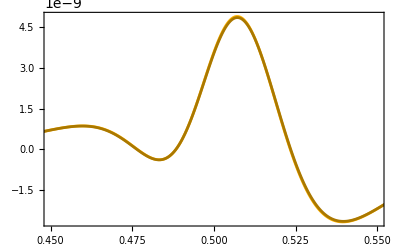

```mathematica
ComponenteTransversalNTSPA=ListPlot[{Transpose[{dataNTSPA[[All,1]],dataNTSPA[[All,2]]}],Transpose[{data1[[All,1]],data1[[All,2]]}]},PlotRange->{{0.45,0.55},All},PlotStyle->{Amarillo,Darker[Amarillo]},Joined->True,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["c(\\hbar\\alpha)^{-1}F_\\perp^\\text{ret}(t)\\text{ [PHz]}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{ NTSPA}",FontSize->8],MaTeX["\\text{  Multi.}",FontSize->8]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->-0.3,LegendMargins->-3,LegendMarkerSize->15],{0.83,0.75}]]
```

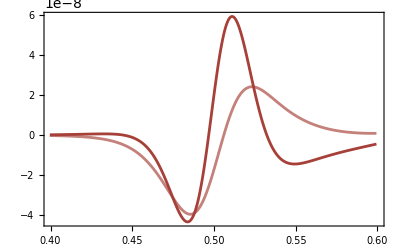

```mathematica
ComponenteTransversalNTSPA=ListPlot[{Transpose[{dataNTSPA[[All,1]],dataNTSPA[[All,4]]}],Transpose[{data2[[All,1]],data2[[All,4]]}]},PlotRange->{{0.4,0.6},All},PlotStyle->{Lighter[Rojo],Rojo},Joined->True,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["c(\\hbar\\alpha)^{-1}F_\\perp^\\text{ret}(t)\\text{ [PHz]}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{ DE-DM}",FontSize->8],MaTeX["\\text{  DE-QE}",FontSize->8],MaTeX["\\text{  Total}",FontSize->8]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->-0.3,LegendMargins->-3,LegendMarkerSize->15],{0.83,0.75}]]
```

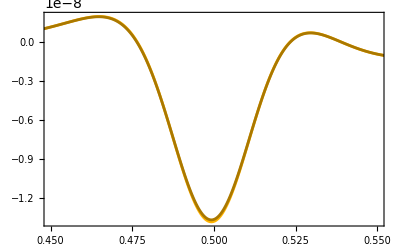

```mathematica
ComponenteLongitudinalNTSPAvsMultiDEDM=ListPlot[{Transpose[{dataNTSPA[[All,1]],dataNTSPA[[All,3]]}],Transpose[{data1[[All,1]],data1[[All,3]]}]},PlotRange->{{0.45,0.55},All},PlotStyle->{Amarillo,Darker[Amarillo]},Joined->True,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["c(\\hbar\\alpha)^{-1}F_\\|^\\text{ret}(t)\\text{ [PHz]}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{ NTSPA}",FontSize->8],MaTeX["\\text{  Multi.}",FontSize->8]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->-0.3,LegendMargins->-3,LegendMarkerSize->15],{0.83,0.75}]]
```

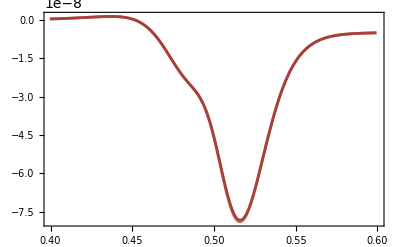

```mathematica
ComponenteLongitudinalNTSPAvsMultiDEQE=ListPlot[{Transpose[{dataNTSPA[[All,1]],dataNTSPA[[All,5]]}],Transpose[{data2[[All,1]],data2[[All,5]]}]},PlotRange->{{0.4,0.6},All},PlotStyle->{Lighter[Rojo],Rojo},Joined->True,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["c(\\hbar\\alpha)^{-1}F_\\|^\\text{ret}(t)\\text{ [PHz]}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{ NTSPA}",FontSize->8],MaTeX["\\text{  Multi.}",FontSize->8],MaTeX["\\text{  Total}",FontSize->8]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->-0.3,LegendMargins->-3,LegendMarkerSize->15],{0.83,0.75}]]
```

Caso ultrarrelativista

```mathematica
dataRel2=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/2.- Recoil Force/Resultados_Fuerza_de_retroceso_n23_T1000_lmax2_a1_b3_beta99.txt","Table"];
dataRel1=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/2.- Recoil Force/Resultados_Fuerza_de_retroceso_n23_T1000_lmax1_a1_b3_beta99.txt","Table"];
```

[1] :	Tiempo
[2] :	Transversal  homopolar
[3] :	Longitudinal  homopolar
[4] :	Transversal  heteropolar  eléctrica
[5] :	Longitudinal  heteropolar  eléctrica
[6] :	Transversal  heteropolar  magnética
[7] :	Longitudinal  heteropolar  magnética
[8] :	Transversal  heteropolar
[9] :	Longitudinal  heteropolar
[10] :	Transversal  total
[11] : Longitudinal  total

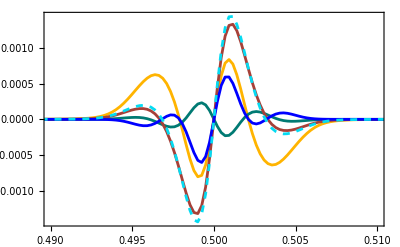

```mathematica
ComponenteTransversalRel=ListPlot[{Transpose[{dataRel1[[All,1]],10^(1(*1*))*dataRel1[[All,2]]}],Transpose[{dataRel2[[All,1]],10^(1(*3*))*(dataRel2[[All,2]]-dataRel1[[All,2]])}],Transpose[{dataRel2[[All,1]],dataRel2[[All,4]]}],Transpose[{dataRel2[[All,1]],10^1 dataRel2[[All,6]]}],Transpose[{dataRel2[[All,1]],dataRel2[[All,2]]+dataRel2[[All,4]]+dataRel2[[All,6]]}]},PlotRange->{{0.49,0.51},All},PlotStyle->{Amarillo,Verde,Rojo,Blue,{Cian,Dashed}},Joined->True,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["c(\\hbar\\alpha)^{-1}F_\\perp^\\text{ret}(t)\\text{ [PHz]}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{  DE-DM }(\\times 10)",FontSize->8],MaTeX["\\text{  QE-QM }(\\times 10)",FontSize->8],MaTeX["\\text{  DE-QE}",FontSize->8],MaTeX["\\text{  DM-QM}(\\times 10)",FontSize->8],MaTeX["\\text{  Total}",FontSize->8]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->-0.3,LegendMargins->-3,LegendMarkerSize->15],{0.83,0.75}]]
```

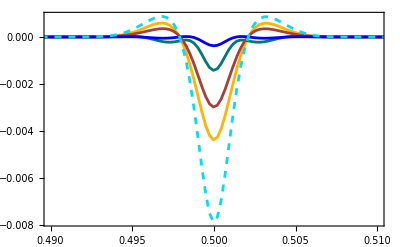

```mathematica
ComponenteLongitudinalRel=ListPlot[{Transpose[{dataRel1[[All,1]],dataRel1[[All,3]]}],Transpose[{dataRel2[[All,1]],10*(dataRel2[[All,3]]-dataRel1[[All,3]])}],Transpose[{dataRel2[[All,1]],dataRel2[[All,5]]}],Transpose[{dataRel2[[All,1]],dataRel2[[All,7]]}],Transpose[{dataRel2[[All,1]],dataRel2[[All,3]]+dataRel2[[All,5]]+dataRel2[[All,7]]}]},PlotRange->{{0.49,0.51},All},PlotStyle->{Amarillo,Verde,Rojo,Blue,{Cian,Dashed}},Joined->True,PlotRange->All,Frame->True, FrameStyle->Thickness[0.005],FrameTicksStyle->Black,FrameLabel->{{MaTeX["c(\\hbar\\alpha)^{-1}F_\\|^\\text{ret}(t)\\text{ [PHz]}",FontSize->16],None},{MaTeX["t\\text{ [fs]}",FontSize->16],None}},LabelStyle->Directive[Black,FontFamily->"Latin Modern Math",FontSize->16],PlotLegends->Placed[LineLegend[{MaTeX["\\text{  DE-DM}",FontSize->8],MaTeX["\\text{  QE-QM }(\\times 10)",FontSize->8],MaTeX["\\text{  DE-QE}",FontSize->8],MaTeX["\\text{  DM-QM}",FontSize->8],MaTeX["\\text{  Total}",FontSize->8]},LegendFunction->(Framed[#,RoundingRadius->3,Background->White]&),Spacings->-0.3,LegendMargins->-3,LegendMarkerSize->15],{0.83,0.25}]]
```

```mathematica
Export["ComponenteTransversalRel.png",ComponenteTransversalRel,ImageResolution->200];
Export["ComponenteLongitudinalRel.png",ComponenteLongitudinalRel,ImageResolution->200];
```

```mathematica
BaseIndices=Import["/home/eduardo/Documentos/Universidad/Licenciatura/Tesis/Datos experimentales/l100-Ii1i2lm-mathematica.dat"];
ToExpression[BaseIndices];
γvel[β_]:=1/(√(1-β^2));
fbar[l_,m_]:=√((2*l+1)*((l-m)!)/((l+m)!));
```

```mathematica
Aast[l_,m_]:=If[m>=0,If[l<m,0,fbar[l,m]*Factorial2[2*l+1]∑_(j=m)^l (ⅈ^(j+Abs[Sin[m*π/2]])/((l-j)!*((j-m)/2)!*((j+m)/2)!(2*γ)^j)II[j,l-j,l,m])],(-1)^-m*Aast[l,-m]];
Bast[l_,m_]:=Aast[l,m+1] √((l-m)(l+m+1))-Aast[l,m-1] √((l+m)(l-m+1));
```

```mathematica
Wast[l_,m_]:=(m*Aast[l,m])/(l(l+1)β^l);
Vast[l_,m_]:=Bast[l,m]/(2l*(l+1)β^(l+1)γ);
```

```mathematica
Rationalize[Vast[2,1]]
```

(-15 √30 (2/15+1/(15 γ^2))-5.47723/γ^2)/(12 β^3 γ)

```mathematica
√(5/6)//N
```

0.912871